```mathematica
Populating the Transition rate matrix U
```

T[n_]:=Table[If[i==j,-β_i,If[i==j+1,β_(i-1),0]],{i,1,n},{j,1,n}]/.β_n→0

```mathematica
MatrixForm[T[5]]
```

(-β_1 | 0 | 0 | 0 | 0
β_1 | -β_2 | 0 | 0 | 0
0 | β_2 | -β_3 | 0 | 0
0 | 0 | β_3 | -β_4 | 0
0 | 0 | 0 | β_4 | 0)

```mathematica
T[n_]:=Table[If[i==j,-Subscript[ϵ, i],If[i==j+1,Subscript[ϵ, i-1],0]],{i,1,n},{j,1,n}]
```

```mathematica
TC[n_]:=ReplacePart[T[n],{{1,n}->Subscript[ϵ, n]}]
```

```mathematica
MatrixForm[TC[5]]
```

(-ϵ_1 | 0 | 0 | 0 | ϵ_5
ϵ_1 | -ϵ_2 | 0 | 0 | 0
0 | ϵ_2 | -ϵ_3 | 0 | 0
0 | 0 | ϵ_3 | -ϵ_4 | 0
0 | 0 | 0 | ϵ_4 | -ϵ_5)

Implementing Q(t)= ⅇ^(αt(u-1)), see eqn. (1) in text

```mathematica
MatrixForm[Simplify[MatrixExp[T[6]]]]
```

(ⅇ^-ϵ_1 | 0 | 0 | 0 | 0 | 0
-((ⅇ^-ϵ_1-ⅇ^-ϵ_2) ϵ_1)/(ϵ_1-ϵ_2) | ⅇ^-ϵ_2 | 0 | 0 | 0 | 0
(ⅇ^(-ϵ_1-ϵ_2-ϵ_3) ϵ_1 ϵ_2 (ⅇ^ϵ_1 (ⅇ^ϵ_2-ⅇ^ϵ_3) ϵ_1-ⅇ^ϵ_2 (ⅇ^ϵ_1-ⅇ^ϵ_3) ϵ_2+ⅇ^ϵ_3 (ⅇ^ϵ_1-ⅇ^ϵ_2) ϵ_3))/((ϵ_1-ϵ_2) (ϵ_1-ϵ_3) (ϵ_2-ϵ_3)) | -((ⅇ^-ϵ_2-ⅇ^-ϵ_3) ϵ_2)/(ϵ_2-ϵ_3) | ⅇ^-ϵ_3 | 0 | 0 | 0
ϵ_1 ϵ_2 ϵ_3 (-ⅇ^-ϵ_1/((ϵ_1-ϵ_2) (ϵ_1-ϵ_3) (ϵ_1-ϵ_4))+ⅇ^-ϵ_2/((ϵ_1-ϵ_2) (ϵ_2-ϵ_3) (ϵ_2-ϵ_4))-ⅇ^-ϵ_3/((-ϵ_1+ϵ_3) (-ϵ_2+ϵ_3) (ϵ_3-ϵ_4))+ⅇ^-ϵ_4/((ϵ_1-ϵ_4) (-ϵ_2+ϵ_4) (-ϵ_3+ϵ_4))) | (ⅇ^(-ϵ_2-ϵ_3-ϵ_4) ϵ_2 ϵ_3 (ⅇ^ϵ_2 (ⅇ^ϵ_3-ⅇ^ϵ_4) ϵ_2-ⅇ^ϵ_3 (ⅇ^ϵ_2-ⅇ^ϵ_4) ϵ_3+ⅇ^ϵ_4 (ⅇ^ϵ_2-ⅇ^ϵ_3) ϵ_4))/((ϵ_2-ϵ_3) (ϵ_2-ϵ_4) (ϵ_3-ϵ_4)) | -((ⅇ^-ϵ_3-ⅇ^-ϵ_4) ϵ_3)/(ϵ_3-ϵ_4) | ⅇ^-ϵ_4 | 0 | 0
ϵ_1 ϵ_2 ϵ_3 ϵ_4 (ⅇ^-ϵ_1/((ϵ_1-ϵ_2) (ϵ_1-ϵ_3) (ϵ_1-ϵ_4) (ϵ_1-ϵ_5))+ⅇ^-ϵ_2/((-ϵ_1+ϵ_2) (ϵ_2-ϵ_3) (ϵ_2-ϵ_4) (ϵ_2-ϵ_5))+ⅇ^-ϵ_3/((-ϵ_1+ϵ_3) (-ϵ_2+ϵ_3) (ϵ_3-ϵ_4) (ϵ_3-ϵ_5))+ⅇ^-ϵ_4/((-ϵ_1+ϵ_4) (-ϵ_2+ϵ_4) (-ϵ_3+ϵ_4) (ϵ_4-ϵ_5))+ⅇ^-ϵ_5/((-ϵ_1+ϵ_5) (-ϵ_2+ϵ_5) (-ϵ_3+ϵ_5) (-ϵ_4+ϵ_5))) | ϵ_2 ϵ_3 ϵ_4 (-ⅇ^-ϵ_2/((ϵ_2-ϵ_3) (ϵ_2-ϵ_4) (ϵ_2-ϵ_5))+ⅇ^-ϵ_3/((ϵ_2-ϵ_3) (ϵ_3-ϵ_4) (ϵ_3-ϵ_5))-ⅇ^-ϵ_4/((-ϵ_2+ϵ_4) (-ϵ_3+ϵ_4) (ϵ_4-ϵ_5))+ⅇ^-ϵ_5/((ϵ_2-ϵ_5) (-ϵ_3+ϵ_5) (-ϵ_4+ϵ_5))) | (ⅇ^(-ϵ_3-ϵ_4-ϵ_5) ϵ_3 ϵ_4 (ⅇ^ϵ_3 (ⅇ^ϵ_4-ⅇ^ϵ_5) ϵ_3-ⅇ^ϵ_4 (ⅇ^ϵ_3-ⅇ^ϵ_5) ϵ_4+ⅇ^ϵ_5 (ⅇ^ϵ_3-ⅇ^ϵ_4) ϵ_5))/((ϵ_3-ϵ_4) (ϵ_3-ϵ_5) (ϵ_4-ϵ_5)) | -((ⅇ^-ϵ_4-ⅇ^-ϵ_5) ϵ_4)/(ϵ_4-ϵ_5) | ⅇ^-ϵ_5 | 0
ϵ_1 ϵ_2 ϵ_3 ϵ_4 ϵ_5 (-ⅇ^-ϵ_1/((ϵ_1-ϵ_2) (ϵ_1-ϵ_3) (ϵ_1-ϵ_4) (ϵ_1-ϵ_5) (ϵ_1-ϵ_6))-ⅇ^-ϵ_2/((-ϵ_1+ϵ_2) (ϵ_2-ϵ_3) (ϵ_2-ϵ_4) (ϵ_2-ϵ_5) (ϵ_2-ϵ_6))-ⅇ^-ϵ_3/((-ϵ_1+ϵ_3) (-ϵ_2+ϵ_3) (ϵ_3-ϵ_4) (ϵ_3-ϵ_5) (ϵ_3-ϵ_6))+ⅇ^-ϵ_4/((ϵ_1-ϵ_4) (-ϵ_2+ϵ_4) (-ϵ_3+ϵ_4) (ϵ_4-ϵ_5) (ϵ_4-ϵ_6))+ⅇ^-ϵ_5/((ϵ_1-ϵ_5) (-ϵ_2+ϵ_5) (-ϵ_3+ϵ_5) (-ϵ_4+ϵ_5) (ϵ_5-ϵ_6))+ⅇ^-ϵ_6/((ϵ_1-ϵ_6) (-ϵ_2+ϵ_6) (-ϵ_3+ϵ_6) (-ϵ_4+ϵ_6) (-ϵ_5+ϵ_6))) | ϵ_2 ϵ_3 ϵ_4 ϵ_5 (ⅇ^-ϵ_2/((ϵ_2-ϵ_3) (ϵ_2-ϵ_4) (ϵ_2-ϵ_5) (ϵ_2-ϵ_6))+ⅇ^-ϵ_3/((-ϵ_2+ϵ_3) (ϵ_3-ϵ_4) (ϵ_3-ϵ_5) (ϵ_3-ϵ_6))+ⅇ^-ϵ_4/((-ϵ_2+ϵ_4) (-ϵ_3+ϵ_4) (ϵ_4-ϵ_5) (ϵ_4-ϵ_6))+ⅇ^-ϵ_5/((-ϵ_2+ϵ_5) (-ϵ_3+ϵ_5) (-ϵ_4+ϵ_5) (ϵ_5-ϵ_6))+ⅇ^-ϵ_6/((-ϵ_2+ϵ_6) (-ϵ_3+ϵ_6) (-ϵ_4+ϵ_6) (-ϵ_5+ϵ_6))) | ϵ_3 ϵ_4 ϵ_5 (-ⅇ^-ϵ_3/((ϵ_3-ϵ_4) (ϵ_3-ϵ_5) (ϵ_3-ϵ_6))+ⅇ^-ϵ_4/((ϵ_3-ϵ_4) (ϵ_4-ϵ_5) (ϵ_4-ϵ_6))-ⅇ^-ϵ_5/((-ϵ_3+ϵ_5) (-ϵ_4+ϵ_5) (ϵ_5-ϵ_6))+ⅇ^-ϵ_6/((ϵ_3-ϵ_6) (-ϵ_4+ϵ_6) (-ϵ_5+ϵ_6))) | (ⅇ^(-ϵ_4-ϵ_5-ϵ_6) ϵ_4 ϵ_5 (ⅇ^ϵ_4 (ⅇ^ϵ_5-ⅇ^ϵ_6) ϵ_4-ⅇ^ϵ_5 (ⅇ^ϵ_4-ⅇ^ϵ_6) ϵ_5+ⅇ^ϵ_6 (ⅇ^ϵ_4-ⅇ^ϵ_5) ϵ_6))/((ϵ_4-ϵ_5) (ϵ_4-ϵ_6) (ϵ_5-ϵ_6)) | -((ⅇ^-ϵ_5-ⅇ^-ϵ_6) ϵ_5)/(ϵ_5-ϵ_6) | ⅇ^-ϵ_6)

```mathematica
Q[n_]:=Table[If[i==j,Exp[-Subscript[β, i]],If[i<j,0,If[i>j,(-1)^(j+i)( ∏_(k=j)^(i-1) Subscript[β, k])*∑_(m=j)^i Exp[-Subscript[β, m]]/((∏_(p=1)^(i-m) (Subscript[β, m]-Subscript[β, m+p]))(∏_(q=j)^(m-1) (Subscript[β, m]-Subscript[β, q])))]]]/.Subscript[β, n]->0,{i,1,n},{j,1,n}]
MatrixForm[Q[6]]
```

(ⅇ^-β_1 | 0 | 0 | 0 | 0 | 0
-β_1 (ⅇ^-β_1/(β_1-β_2)+ⅇ^-β_2/(-β_1+β_2)) | ⅇ^-β_2 | 0 | 0 | 0 | 0
β_1 β_2 (ⅇ^-β_1/((β_1-β_2) (β_1-β_3))+ⅇ^-β_2/((-β_1+β_2) (β_2-β_3))+ⅇ^-β_3/((-β_1+β_3) (-β_2+β_3))) | -β_2 (ⅇ^-β_2/(β_2-β_3)+ⅇ^-β_3/(-β_2+β_3)) | ⅇ^-β_3 | 0 | 0 | 0
-β_1 β_2 β_3 (ⅇ^-β_1/((β_1-β_2) (β_1-β_3) (β_1-β_4))+ⅇ^-β_2/((-β_1+β_2) (β_2-β_3) (β_2-β_4))+ⅇ^-β_3/((-β_1+β_3) (-β_2+β_3) (β_3-β_4))+ⅇ^-β_4/((-β_1+β_4) (-β_2+β_4) (-β_3+β_4))) | β_2 β_3 (ⅇ^-β_2/((β_2-β_3) (β_2-β_4))+ⅇ^-β_3/((-β_2+β_3) (β_3-β_4))+ⅇ^-β_4/((-β_2+β_4) (-β_3+β_4))) | -β_3 (ⅇ^-β_3/(β_3-β_4)+ⅇ^-β_4/(-β_3+β_4)) | ⅇ^-β_4 | 0 | 0
β_1 β_2 β_3 β_4 (ⅇ^-β_1/((β_1-β_2) (β_1-β_3) (β_1-β_4) (β_1-β_5))+ⅇ^-β_2/((-β_1+β_2) (β_2-β_3) (β_2-β_4) (β_2-β_5))+ⅇ^-β_3/((-β_1+β_3) (-β_2+β_3) (β_3-β_4) (β_3-β_5))+ⅇ^-β_4/((-β_1+β_4) (-β_2+β_4) (-β_3+β_4) (β_4-β_5))+ⅇ^-β_5/((-β_1+β_5) (-β_2+β_5) (-β_3+β_5) (-β_4+β_5))) | -β_2 β_3 β_4 (ⅇ^-β_2/((β_2-β_3) (β_2-β_4) (β_2-β_5))+ⅇ^-β_3/((-β_2+β_3) (β_3-β_4) (β_3-β_5))+ⅇ^-β_4/((-β_2+β_4) (-β_3+β_4) (β_4-β_5))+ⅇ^-β_5/((-β_2+β_5) (-β_3+β_5) (-β_4+β_5))) | β_3 β_4 (ⅇ^-β_3/((β_3-β_4) (β_3-β_5))+ⅇ^-β_4/((-β_3+β_4) (β_4-β_5))+ⅇ^-β_5/((-β_3+β_5) (-β_4+β_5))) | -β_4 (ⅇ^-β_4/(β_4-β_5)+ⅇ^-β_5/(-β_4+β_5)) | ⅇ^-β_5 | 0
-β_1 β_2 β_3 β_4 β_5 (ⅇ^-β_1/(β_1 (β_1-β_2) (β_1-β_3) (β_1-β_4) (β_1-β_5))+ⅇ^-β_2/(β_2 (-β_1+β_2) (β_2-β_3) (β_2-β_4) (β_2-β_5))+ⅇ^-β_3/(β_3 (-β_1+β_3) (-β_2+β_3) (β_3-β_4) (β_3-β_5))+ⅇ^-β_4/(β_4 (-β_1+β_4) (-β_2+β_4) (-β_3+β_4) (β_4-β_5))-1/(β_1 β_2 β_3 β_4 β_5)+ⅇ^-β_5/(β_5 (-β_1+β_5) (-β_2+β_5) (-β_3+β_5) (-β_4+β_5))) | β_2 β_3 β_4 β_5 (ⅇ^-β_2/(β_2 (β_2-β_3) (β_2-β_4) (β_2-β_5))+ⅇ^-β_3/(β_3 (-β_2+β_3) (β_3-β_4) (β_3-β_5))+ⅇ^-β_4/(β_4 (-β_2+β_4) (-β_3+β_4) (β_4-β_5))+1/(β_2 β_3 β_4 β_5)+ⅇ^-β_5/(β_5 (-β_2+β_5) (-β_3+β_5) (-β_4+β_5))) | -β_3 β_4 β_5 (ⅇ^-β_3/(β_3 (β_3-β_4) (β_3-β_5))+ⅇ^-β_4/(β_4 (-β_3+β_4) (β_4-β_5))-1/(β_3 β_4 β_5)+ⅇ^-β_5/(β_5 (-β_3+β_5) (-β_4+β_5))) | β_4 β_5 (ⅇ^-β_4/(β_4 (β_4-β_5))+1/(β_4 β_5)+ⅇ^-β_5/(β_5 (-β_4+β_5))) | -(-1/β_5+ⅇ^-β_5/β_5) β_5 | 1)

The entries of matrix Q(t) for any arbitrary value of n is given by

```mathematica
R[i_,j_,n_]:=(-1)^(j+i)*( ∏_(k=j)^(i-1) γ[[k,n]])*∑_(m=j)^i Exp[-γ[[m,n]]]/((∏_(p=1)^(i-m) (γ[[m,n]]- γ[[m+p,n]]))(∏_(q=j)^(m-1) (γ[[m,n]]-γ[[q,n]])))
```

```mathematica
filt[nn0_,γ0_]:=Module[{nn=nn0,γ=γ0},
thres=1*^-6;
qq=Transpose[γ];qq1=Sort/@qq;qq2=Differences[qq1,{0,1}];
qq3=Min/@qq2;qq4=Transpose[Join[Transpose[qq],{qq3}]];
qq5=Select[qq4,#[[31]]>thres&];
γ=Transpose[qq5[[1;;nn,1;;30]]];
γ
]
```

```mathematica
createDist[nn0_,dist0_]:=Module[{nn=nn0,dist=dist0},
nk=2*nn;
γ={RandomVariate[dist,nk]};
For[i=0,i<29,i++,q=RandomVariate[dist,nk];
γ=Join[γ,{q}]];
γ=filt[nn,γ];
γ
]
```

Numerical calculation of the final column (representing the termination state - the distribution of released protein for the ensemble at any specific time t=T) 
of matrix Q(t) for n=30 with an ensemble of size 25,000 where ε ’s are normally distributed

```mathematica
nn=25000;
```

```mathematica
dist=NormalDistribution[50,15];
```

```mathematica
γ=createDist[nn,dist];
```

```mathematica
m=Table[R[30,1,i],{i,nn}];
```

```mathematica
m1Normal=Select[m,1>#>0&];
```

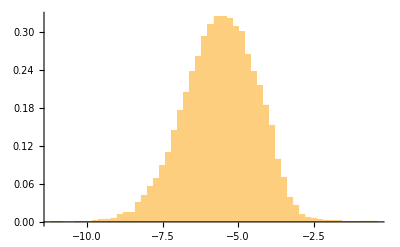

```mathematica
P1=Histogram[Log[m1Normal],50,"ProbabilityDensity"]
```

Numerical calculation of the final column entries of matrix Q(t) for n=30 with an ensemble of size 25,000 where ε ’s are normally distributed

```mathematica
dist=GammaDistribution[10,5];
```

```mathematica
γ=createDist[nn,dist];
```

```mathematica
m=Table[R[30,1,i],{i,nn}];
```

```mathematica
m1Gamma=Select[m,1>#>0&];
```

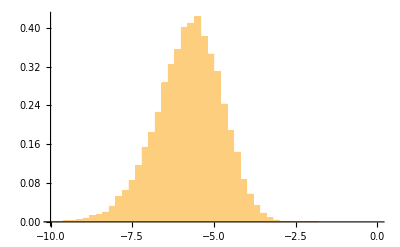

```mathematica
Q1=Histogram[Log[m1Gamma],65,"ProbabilityDensity",AxesOrigin->{-10,0},PlotRange->{{-10,0},All}]
```

```mathematica
ClearSystemCache[]
```